# Apriori Algorithm

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Data

```mathematica
(* Data definition *)
Subscript[x, 1]={"Beer","Nappies","Tomatoes"};
Subscript[x, 2]={"Beer","Nappies","Crisps"};
Subscript[x, 3]={"Crisps"};
Subscript[x, 4]={"Beer","Nappies","Crisps"};

M=4;
X=Table[Subscript[x, i],{i,1,M}];(* List with all transactions *)
Subscript[s, min]=0.4;
Subscript[k, min]=0.8;(* Reduce the rule output *)
```

## Algorithm

### Implementation

```mathematica
(* Functions *)
support[Y_]:=Count[X,i_/;ContainsAll[i,Y]]/M;(* Count each transaction which covers Y completely *)
confidence[Y_,Z_]:=support[Y∪Z]/support[Y];

step2CalcSupport[]:=(
(* Each element from Subscript[H, n] with it's support *)
Subscript[S, n]=({#,support[#]})&/@Subscript[H, n]//N;
);
step3MinSupport[]:=(
(* Keep only elements from Subscript[H, n] which fulfill the support condition *)
Subscript[Ι, n]=Cases[Subscript[H, n],Y_/;support[Y]≥Subscript[s, min]];
Print[ToString[Subscript["Ι",n],StandardForm]<>" = "<>ToString[Subscript[Ι, n],StandardForm]];
);
step4Merge[]:=(
ℐ=ℐ∪Subscript[Ι, n];
Print["ℐ = "<>ToString[ℐ,StandardForm]];
);
step5SizeIncrease[]:=(
(* Find next elements *)
Subscript[H, n+1]=Union[Sort[(* Keep a sorted list without duplicates *)
Cases[
Flatten[Outer[(Flatten@{#1∪#2})&,Subscript[Ι, 1],Subscript[Ι, n],1],1],(* Cartesian cross product between Subscript[Ι, n] and Subscript[Ι, 1] *)
Y_/;Length[Y]≥n+1(* Keep only elements with proper length *)
]
]];
Print[ToString[Subscript["H",n+1],StandardForm]<>" = "<>ToString[Subscript[H, n+1],StandardForm]];
);
step6Increment[]:=(
++n;
Print["n = "<>ToString[n,StandardForm]];
);
```

### Step 1

```mathematica
n=1;
ℐ={};
Subscript[H, 1]=({#})&/@Union[Flatten[X,1]]
```

{{Beer},{Crisps},{Nappies},{Tomatoes}}

```mathematica
While[True,
step2CalcSupport[];
step3MinSupport[];
If[Length[Subscript[Ι, n]]==0,
Print["Algorithm terminated"];
Break[]
];
step4Merge[];
step5SizeIncrease[];
step6Increment[];
]
```

Ι_1 = {{Beer},{Crisps},{Nappies}}

ℐ = {{Beer},{Crisps},{Nappies}}

H_2 = {{Beer,Crisps},{Beer,Nappies},{Crisps,Nappies}}

n = 2

Ι_2 = {{Beer,Crisps},{Beer,Nappies},{Crisps,Nappies}}

ℐ = {{Beer},{Crisps},{Nappies},{Beer,Crisps},{Beer,Nappies},{Crisps,Nappies}}

H_3 = {{Beer,Crisps,Nappies}}

n = 3

Ι_3 = {{Beer,Crisps,Nappies}}

ℐ = {{Beer},{Crisps},{Nappies},{Beer,Crisps},{Beer,Nappies},{Crisps,Nappies},{Beer,Crisps,Nappies}}

H_4 = {}

n = 4

Ι_4 = {}

Algorithm terminated

```mathematica
popularSets=(#->support[#]&)/@ℐ;
SortBy[popularSets,#[[2]]&]//TableForm
```

{Beer,Crisps}→1/2
{Crisps,Nappies}→1/2
{Beer,Crisps,Nappies}→1/2
{Beer}→3/4
{Crisps}→3/4
{Nappies}→3/4
{Beer,Nappies}→3/4

### Step 2

```mathematica
rules=Flatten[
((* Iterate over each element in ℐ *)
Module[{element,singleElements,singleElement,compl,konf,result={}},
element=#;(* {"Drucker","Hut","Schal"} *)

Do[
(* All i-th parts of the current element:
i=1: {{"Drucker"},{"Hut"},{"Schal"}} and
i=2: {{"Drucker","Hut"},{"Drucker","Schal"},{"Hut","Schal"}}
*)
singleElements=Subsets[element,{i}];

((* Iterate over each element in the subset, place each element on the right side *)
singleElement=#;(* {"Drucker"} *)
compl=Complement[element,singleElement];(* {"Hut","Schal"} *)
konf=confidence[compl,singleElement];(* {"Hut","Schal"} -> {"Drucker"} *)
AppendTo[result,{compl->singleElement,konf}];
)&/@singleElements;

,{i,1,Length[element]-1}];

result
]
)&/@Cases[ℐ,Y_/;Length[Y]≥2],1]//N;
```

All rules:

```mathematica
rules//TableForm
```

{Crisps}→{Beer} | 0.666667
{Beer}→{Crisps} | 0.666667
{Nappies}→{Beer} | 1.
{Beer}→{Nappies} | 1.
{Nappies}→{Crisps} | 0.666667
{Crisps}→{Nappies} | 0.666667
{Crisps,Nappies}→{Beer} | 1.
{Beer,Nappies}→{Crisps} | 0.666667
{Beer,Crisps}→{Nappies} | 1.
{Nappies}→{Beer,Crisps} | 0.666667
{Crisps}→{Beer,Nappies} | 0.666667
{Beer}→{Crisps,Nappies} | 0.666667

Only rules which fulfil the confidence constraint:

```mathematica
Cases[
SortBy[rules,#[[2]]&],
Y_/;Y[[2]]≥Subscript[k, min]
]//TableForm
```

{Beer}→{Nappies} | 1.
{Nappies}→{Beer} | 1.
{Beer,Crisps}→{Nappies} | 1.
{Crisps,Nappies}→{Beer} | 1.

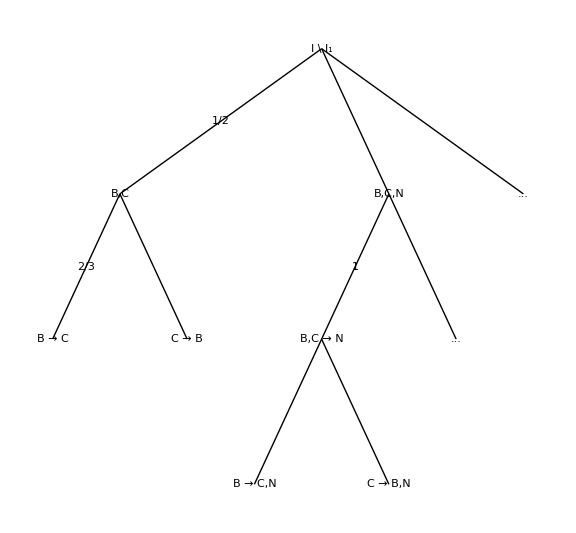

```mathematica
reLabelF[verts_,labels_][tp_]:=tp/.(Framed[#,p__]:>Framed[#2,p]&@@@Transpose[{verts,labels}])

labels={
Row[{it["I"]," \\ ","I_1"}],
Row[{it["B"],",",it["C"]}],
Row[{it["B"],",",it["C"],",",it["N"]}],
"...",
Row[{it["B"]," → ",it["C"]}],
Row[{it["C"]," → ",it["B"]}],
Row[{it["B"],",",it["C"]," → ",it["N"]}],
"...",
Row[{it["B"]," → ",it["C"],",",it["N"]}],
Row[{it["C"]," → ",it["B"],",",it["N"]}]
};

TreePlot[{
{1->2,1/2},
1->3,
1->4,
{2->5,2/3},
2->6,
{3->7,1},
3->8,
7->9,
7->10
},
VertexLabeling->True,
ImageSize->Large,
EdgeRenderingFunction->({Thick,Line[#1],If[#3===None,{},Text[Panel@StandardForm@Style[#3,Piecewise[{{RGBColor[0.368417, 0.506779, 0.709798], #3==1/2}, {RGBColor[0.915, 0.3325, 0.2125], True}}],FontFamily->"Libertinus Serif",FontSize->18],Mean@#1]]}&)
]//reLabelF[Range[10],Style[#,22,FontFamily->"Libertinus Serif"]&/@labels]
```

## Supplementary questions

We can see from the transaction table that the minimum confidence is 2/3 for possible rules of I (this is also confirmed by the results above). To get a small value for the confidence, we need the numerator to be as small as possible and the denominator to be as large as possible, i.e.

conf(X→Y)=(support(X∪Y))/(support(X))⇒(as small as possible)/(as large as possible)⇒0.4/0.6=2/3

support(X∪Y)=2/5 because in all combinations of {B,N,C} at least two transactions remain.

support(X)=3/5 because each item is not bought more than three times (X must be a single-item set since more items can only decrease the support).

The rules C→T and T→C have both a confidence value of 0 since the two items do not co-occur.